# Chapter. Monte Carlo simulations

files used:
monteCarloLSV.dat
monteCarloChrono.dat
cvRev.dat

In this notebook you are asked to load data from the SERM/Data folder. To prepare for this copy the line below to an input cell, replace the file path with the file path for the "Data" folder on your computer and press ⌤
AppendTo[$Path,”(* path to *)/SERM/Data/chapter12”];
or
AppendTo[$Path,ToFileName[ {NotebookDirectory[],”Data”,”chapter12”}]];

Mathematica Preliminaries

### General

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"]];
```

```mathematica
AppendTo[$Path,ToFileName[ {NotebookDirectory[],"Data","chapter12"}]];

$Path=Union[$Path];
```

```mathematica
SetSystemOptions["TypesetOptions"->{"IconicElidedForms"->False}];
```

```mathematica
CurrentValue[$FrontEnd,{SpellingDictionaries,"CorrectWords"}]=Union@Join[CurrentValue[$FrontEnd,{SpellingDictionaries,"CorrectWords"}],{"Bioanalytical","chronoamperogram","chronoamperometric","Chronoamperometric","chronoamperometry","Chronoamperometry","chronopotentiogram","chronopotentiometric","chronopotentiometry","electroactive","electroanalytical","electrochemists","eqn","eqns","Faradaic","Feldberg","Fick's","kth","Louiville","Nernst","Nicolson","overpotential","overpotentials","Richtmyer","Rieman","Semiintegration","Volmer","voltammetric","Voltammetric","voltammetry","voltammogram","voltammograms"}];
```

```mathematica
SetOptions[Plot,
Axes-> False,
BaseStyle->Directive[FontFamily-> "Arial",10,Plain],
Frame->True,
FrameLabel-> None,
FrameStyle->Directive[Black,AbsoluteThickness[.5]],
GridLines->None,
ImagePadding->{{Inherited,5},{Inherited,5}},
ImageSize->288,
PlotStyle->Directive[Black,AbsoluteThickness[.5]]];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
BaseStyle->Directive[FontFamily-> "Arial",10,Plain],
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[.5]],
GridLines->None,
ImagePadding->{{Inherited,5},{Inherited,5}},
ImageSize->288,
Joined->True,
PlotLabel->None,
PlotStyle->Directive[Black,AbsoluteThickness[.5]]];
```

```mathematica
SetOptions[ListLogPlot,
BaseStyle->Directive[FontFamily->"Arial",10,Plain],
FrameStyle->Directive[Black,AbsoluteThickness[.5]],
ImagePadding->{{Inherited,5},{Inherited,5}},
ImageSize->288,
LabelStyle->Directive[FontFamily->"Arial",10,Plain],
PlotStyle->AbsolutePointSize[5],
Joined->False];
```

```mathematica
SetOptions[ListLogLogPlot,
Axes->False,
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[.5]],
GridLines->None,
ImageSize->288,
LabelStyle->Directive[FontFamily->"Arial",10,Plain],
PlotStyle->Directive[Black,AbsoluteThickness[.5]],
Joined->True,
RotateLabel-> False];
```

```mathematica
SetOptions[Histogram,
Frame-> True,
ImagePadding->{{Inherited,5},{Inherited,5}},
ChartStyle->Directive[Black,HatchFilling[]]
];
```

```mathematica
SetOptions[Plot3D,
AspectRatio-> 1,
AxesEdge->{{1,-1},{-1,-1},{1,1}},
AxesStyle->AbsoluteThickness[1],
Boxed-> True,
BoxRatios->{1,1,.7},
BoxStyle->AbsoluteDashing[{2.5,2.5}],
ImageSize->288,
Lighting-> Automatic,
Mesh->False,
PlotRange->All,
ViewVertical->{0,0,1},
ViewPoint->{2,-.5,1}];
```

```mathematica
SetOptions[ListPlot3D,
AspectRatio-> 1,
Axes->True,
AxesEdge->{{-1,-1},{1,-1},{1,1}},
AxesStyle->AbsoluteThickness[1],
Boxed-> True,
BoxRatios->{1,1,.7},
BoxStyle->AbsoluteDashing[{2.5,2.5}],
ImageSize->288,
LabelStyle->Directive[FontFamily->"Arial",10,Plain],
Lighting-> Automatic,
Mesh->False,
PlotRange->All,
ViewVertical->{0,0,1},
ViewPoint->{2,-.5,1}];
```

```mathematica
(* tick function for labelled axes or frames *)
ticks1[min_,max_,steps_,divs_]:=Join[Table[{x,Which[
Chop[x]==0,0,
0<x<2,NumberForm[x,{2,2},NumberPadding->{"","0"}],
x≥2,NumberForm[x,{2,0},NumberPadding->{"","0"}],
0>x≥-2,NumberForm[x,{2,2},NumberPadding->{"0","0"}],
-2>x,NumberForm[x,{2,0},NumberPadding->{"","0"}]
],{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]];

(* tick function for non-labelled axes or frames *)
ticks2[min_,max_,steps_,divs_]:=Chop[Join[Table[{x,"",{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]]];
```

```mathematica
ClearAll[LowerDiagonalMatrix,UpperDiagonalMatrix];

LowerDiagonalMatrix[f_,n_Integer?NonNegative]:=Array[If[#≥#2,f[##],0]&,{n,n}];
UpperDiagonalMatrix[f_,n_Integer?NonNegative]:=Array[If[#≤#2,f[##],0]&,{n,n}];
```

```mathematica
ClearAll[𝒻,F,R,T];
F=N@QuantityMagnitude@EntityValue[Entity["PhysicalConstant","FaradayConstant"],"Value"];(*Faradays constant*)
R=N@QuantityMagnitude@EntityValue[Entity["PhysicalConstant","MolarGasConstant"],"Value"];(*gas constant*)
T = 298.;
𝒻=F/(R*T);
```

```mathematica
Unprotect[InverseLaplaceTransform];
InverseLaplaceTransform[i_[s]/(√s), s_, t_] := 1/(√π)*∫_0^t i[τ]/(√(t-τ))ⅆτ;

(*Protect[InverseLaplaceTransform];*)
```

This for Mathematica Version 4.0 and above

```mathematica
If[$VersionNumber>3.,
Unprotect[LaplaceTransform];

LaplaceTransform[Derivative[d__][c][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][C[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];
LaplaceTransform[Derivative[d__][u][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][U[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];
LaplaceTransform[Derivative[d__][v][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][V[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];
LaplaceTransform[c[args__],t_,s_]:=With[{pos=Position[{args},t]},C[s][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1]

(*Protect[LaplaceTransform];*)];
```

### Notebook

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[EvaluationNotebook[],
PrintingStartingPageNumber->211,

PageHeaders-> {
{Cell[TextData[{CounterBox["Page"]}],FontFamily->"Arial",FontSize->12], Cell[TextData[{"Monte Carlo simulations"}],FontFamily->"Arial",FontSize->12],None},
{None,Cell[TextData[CounterBox["Section",CounterFunction:>(Part[{"Introduction","Random walks","Simulating electrochemical reactions"},#]&)]],FontFamily->"Arial",FontSize->12],Cell[TextData[{CounterBox["Page"]}],FontFamily->"Arial",FontSize->12]}},

PageFooters->{{None,None,None},{None,None,None}},
PrintingOptions-> {
"PrintingMargins"->{{90,90},{60,90}},
"PaperSize"->{596,794},
"PageSize"->{596,794},
"PageHeaderMargins"->{60,60},
"PageFooterMargins"->{30,30},
"GraphicsPrintingFormat"->"DownloadPostScript",
"FirstPageFace"->Right,
"FirstPageHeader"->False,
"FirstPageFooter"->False,
"PrintRegistrationMarks"-> False}];
```

```mathematica
option1={
FrameTicks->{ticks1[-25,25,5,5],ticks1[0,.3,.1,5],ticks2[-25,25,5,5],ticks2[0,.3,.1,5]},
FrameLabel-> {
Style["x",FontFamily-> "Times New Roman",12,Italic],
Style["P",FontFamily-> "Times New Roman",12,Italic],
None,None}
};
```

```mathematica
option1a={
FrameTicks->{ticks1[-40,40,10,5],ticks1[0,.03,.01,5],ticks2[-40,40,10,5],ticks2[0,.03,.01,5]},
FrameLabel-> {
Style["x",FontFamily-> "Times New Roman",12,Italic],
Style["P",FontFamily-> "Times New Roman",12,Italic],
None,None}
};
```

```mathematica
option2={
Joined->True,
FrameTicks-> {Automatic,Automatic,None,None},
FrameLabel-> {Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",10,Italic],None,None,None}
};
```

```mathematica
option3={
Joined->False,
PlotStyle->Directive[Black,AbsolutePointSize[1]],
FrameTicks->{Automatic,None,None,None},
FrameLabel->{"time",None,None,None}
};
```

```mathematica
option4={
Joined-> False,
PlotStyle-> Directive[Black,AbsolutePointSize[3]],
FrameTicks->{ticks1[-10,10,5,5],ticks1[-20,40,5,5],ticks2[-10,10,5,5],ticks2[-20,40,5,5]},
FrameLabel-> {Style["nF/RT(E-E)",FontFamily-> "Times New Roman",10,Italic],None,None,None}
};
```

```mathematica
option5={
PlotRange-> {{-10,10},{10,-700}},
FrameTicks->{ticks1[-25,25,5,5],ticks1[0,-700,-200,5],ticks2[-25,25,5,5],ticks2[0,-700,-200,5]},
FrameLabel-> {Style["nF/RT(E-E)",FontFamily-> "Times New Roman",10,Italic],None,None,None}
};
```

```mathematica
option6={
PlotRange-> {{-10,10},{0.1,-1.1}},
PlotStyle-> Black,
FrameTicks->{ticks1[-25,25,5,5],ticks1[0,-2,-.5,5],ticks2[-25,25,5,5],ticks2[0,-2,-.5,5]},
FrameLabel-> {Style["nF/RT(E-E)",FontFamily-> "Times New Roman",10,Italic],None,None,None}
};
```

```mathematica
option7={
FrameTicks->{ticks1[0,400,100,5],ticks2[0,800,200,5],ticks2[0,400,100,5],ticks2[0,800,200,5]},
PlotRange-> {{0,400},{0,800}},
FrameLabel-> {Style["t",FontFamily-> "Times New Roman",10,Italic],None,None,None}
};
```

```mathematica
option8={
FrameTicks->{ticks1[0,10,2,5],ticks1[0,8,2,5],ticks2[0,10,2,5],ticks2[0,8,2,5]},
FrameLabel-> {
DisplayForm[RowBox[{TraditionalForm[MakeBoxes[ln[t],TraditionalForm]]}]],
DisplayForm[RowBox[{TraditionalForm[MakeBoxes[ln[i],TraditionalForm]]}]],
None,None}
};
```

```mathematica
option9={
Joined-> False,
PlotStyle-> Directive[Black,AbsolutePointSize[3]],
PlotRange-> {{5,500},{100,1900}},
FrameLabel-> {
DisplayForm[RowBox[{TraditionalForm[MakeBoxes[ln[t],TraditionalForm]]}]],
DisplayForm[RowBox[{TraditionalForm[MakeBoxes[ln[i],TraditionalForm]]}]],
None,None}
};
```

```mathematica
ClearAll[semiIntD2];

semiIntD2[list_List,τ_]:=Module[{y1,y2,y3,col1,col2},

(* separate the two columns *)
col1=Drop[MapThread[#⟦1⟧&,{list}],-1];col2=MapThread[#⟦2⟧&,{list}];

y1=Table[1/√(Length[col2]-i+0.5), {i, Length[col2],2,-1}];
y2=ListCorrelate[{1,1},col2];
y3=(0.5*√Abs[τ]/√Pi)*ListConvolve[y1,y2,{1,1},0]//N;MapThread[{#1,#2}&,{col1,y3}]]
```

```mathematica
initial=10;
incr=0.05;
rw:=2*RandomInteger[{0,1}]-1;
```

```mathematica
$Line=0;
```

Chapter.Section Introduction

Rather than simulate electrochemical systems analytically or numerically from equations describing bulk properties Monte Carlo methods can be used to perform simulations by gathering statistics using random walks. After showing how to generate random walks in Mathematica we give two examples of electrochemical Monte Carlo simulations, one voltammetric and one chronoamperometric.

## Chapter.Section Random walks

Chapter.Section.Subsection One dimensional random walk

Diffusion is a process that can be modelled as a random walk of molecules in solution with the result being a smoothing out of concentration gradients. This smoothing process can be illustrated by simulating a one dimensional random walk of molecules in which molecules can move one distance unit in each time increment. In a one dimensional random walk the molecule can move either forward (+1) or backward (-1) from its position with equal probability. We begin by writing a function, rw, to generate ±1 randomly.

```mathematica
rw:=2 RandomInteger[{0,1}]-1
```

Next we follow the path of the molecule after a given number of time increments by generating a list of its positions relative to the starting point.

```mathematica
FoldList[ Plus, 0,Table[rw,{20}]]
```

{0,1,2,3,4,5,4,3,2,1,0,1,2,3,4,3,4,3,2,1,2}

In this procedure the Table function generates ±1 a given number of times. For example:

```mathematica
Table[rw,{10}]
```

{-1,-1,-1,1,-1,1,-1,1,-1,-1}

FoldList is used to cumulatively add the numbers generated by the Table. In the example above the function being applied to the list is Plus and the first value in the returned list is 0. If we simply want the final position of the molecule after a certain time we would use Fold instead of FoldList. This returns the last element in the list generated by FoldList. In the procedure below the final position of ten different walkers after twenty time increments is returned.

```mathematica
ClearAll[j,t,positionList];
j=10;(*number of particles/walkers*)
t=20;
positionList=Table[Fold[ Plus, 0,Table[rw,{t}]],{i,1,j}]
```

{0,-4,6,2,-6,0,2,-2,0,0}

The theory of random walks tells us that the probability, P, of a molecule being located at a distance, x, after time t (moving a distance d per time increment τ) will have a Gaussian distribution given by

P(x,t)=((2τ)/πt)^(1/2)exp(-(x^2 τ)/(2 td^2))

The mean square displacement, ⟨Δx^2⟩, of a molecule after time t is

⟨Δx^2⟩=td^2/τ

Therefore the root mean square displacement is proportional to t^(1/2)

Δx_rms∝t^(1/2)

The diffusion coefficient, D, is

D=d^2/(2τ)

In this simulation we are using unit time and distance increments. To test the simulation against theory the distribution of the positions of molecules in the simulated random walk can be plotted. The number of molecules at each distance unit from the starting position must first be counted. The first step is to use Sort to sort the list that we have just generated.

```mathematica
ClearAll[sorted];
sorted=Sort[positionList]
```

{-6,-4,-2,0,0,0,0,2,2,6}

After sorting the list we can now group identical elements within the list into separate sublists with Split.

```mathematica
ClearAll[grouped];
grouped=Split[sorted]
```

{{-6},{-4},{-2},{0,0,0,0},{2,2},{6}}

Combining these two functions into Split[Sort[list]] will therefore create a list that contains sublists of identical elements. We want to determine the frequency of molecules at a particular position, i.e. the number of elements or length of each sub-list. The Map function can be used to apply Length to each sub-list in our list.

To apply Length to each of the sublists in the list we could simply write

```mathematica
Length/@grouped
```

{1,1,1,4,2,1}

However in a moment we’ll combine Length with other functions so for now we’ll create a pure function Function[Length[#]], that in shorthand notation is written as Length[#]&. We can now write a function to perform all the steps discussed above and then determine the frequency of molecules at each position.

```mathematica
ClearAll[frequencies1];
frequencies1[mylist_List]:=Length[#]&/@ mylist
```

```mathematica
frequencies1[grouped]
```

{1,1,1,4,2,1}

We could also create a function that returns the positions that are occupied by molecules at the completion of the random walk. The first element in each of the sublists gives us the position. Therefore we can write an analogous function to that above using First.

```mathematica
ClearAll[position];
position[mylist_List]:=First/@ mylist
```

```mathematica
position[grouped]
```

{-6,-4,-2,0,2,6}

By combining the two functions position and frequencies1 into one we can return the frequency of molecules indexed at each position.

```mathematica
ClearAll[frequencies2];

frequencies2[mylist_List]:={Length[#],First[#]}&/@mylist
```

```mathematica
sorted=Sort[positionList];
grouped=Split[sorted];
frequencies2[grouped]
```

{{1,-6},{1,-4},{1,-2},{4,0},{2,2},{1,6}}

Note that alternative ways to achieve this outcome are possible.

```mathematica
Reverse[Sort[Tally[positionList]],2]
```

{{1,-6},{1,-4},{1,-2},{4,0},{2,2},{1,6}}

Finally we can extend our function further by dividing Length[#] by the number of walkers in the simulation to obtain the fraction of walkers at each position. Additionally mylist is defined as a List. This is not essential but it prevents Mathematica from trying to evaluate the function if a list has not been used as an input.

```mathematica
ClearAll[frequencies3];

frequencies3[list_List,number_Integer]:={First[#],N[Length[#]/number]}&/@Split[Sort[list]]
```

We are now in a position to simulate the one dimensional random walks of a large number of walkers.

```mathematica
ClearAll[number,time,positionList];

number=5000;(*number of walkers*)
time=20;(*number of time steps*)

positionList=Table[Fold[ Plus, 0,Table[rw,{time}]],{i,1,number}];
```

```mathematica
m1=frequencies3[positionList,number]
```

{{-18,0.0002},{-14,0.0008},{-12,0.0056},{-10,0.0096},{-8,0.0328},{-6,0.0862},{-4,0.1238},{-2,0.1556},{0,0.1704},{2,0.1642},{4,0.1218},{6,0.0758},{8,0.0362},{10,0.0136},{12,0.0028},{14,0.0004},{16,0.0002}}

These results can be fitted to a Gaussian curve.

```mathematica
m2=Fit[m1,{Exp[-x^2/(2.*time)]},x]
```

0.178218 ⅇ^(-0.025 x^2)

The equation of best fit, m2, agrees well with eqn (Chapter.EquationNumbered) for t=20, d=1, and τ =1.

```mathematica
Sqrt[2./(Pi*time)]* Exp[-x^2/(2.*time)]
```

0.178412 ⅇ^(-0.025 x^2)

The data points are plotted below along with the curve fit. Rather than manually list all the points in m1 the points are mapped onto the plot.

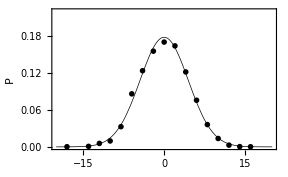

```mathematica
plot1=Plot[m2,{x,-20,20},PlotRange-> {{-20,20},{0,.22}},Evaluate[option1],Epilog->{AbsolutePointSize[4],GrayLevel[0],Map[Point,m1]}]
```

Fig. Chapter.FigureCaption  Simulated probability distribution after a random walk of twenty time steps.

Alternatively a histogram of the data could be plotted.

```mathematica
plota=Histogram[positionList,Automatic,"Probability"];
plotb=Plot[m2,{x,-20,20},PlotStyle->Directive[Black,Thick]];

Show[plota,plotb]
```

-Graphics-

Fig. Chapter.FigureCaption  Histogram of the simulated probability distribution after a random walk of twenty time steps.

The smoothing out of concentration gradients is best illustrated by repeating the simulation at several different time scales. Figure Chapter.FigureCaption shows the results of the simulation. The longer the time scale of the experiment the more uniform the fraction of the walkers at each position, in other words the more uniform the concentration.

```mathematica
ClearAll[diffusion];
(*This function simulates the random walk of n walkers over a period t*)

diffusion[n_,t_]:=Module[{tmp,m1},
tmp=Table[Fold[ Plus, 0,Table[rw,{t}]],{i,1,n}];
m1=frequencies3[tmp,n];
Fit[m1,{Exp[-(x^2)/(2.*1.*t)]},x]
]
```

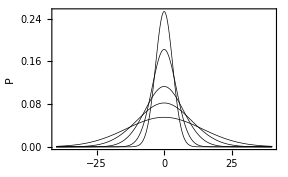

```mathematica
Plot[{
Evaluate[diffusion[500,10]],
Evaluate[diffusion[500,20]],Evaluate[diffusion[500,50]],Evaluate[diffusion[500,100]],Evaluate[diffusion[500,200]]},{x,-40,40},PlotStyle->Directive[Black,AbsoluteThickness[0.5]],PlotRange-> {Automatic,{0,All}},Evaluate[option1a]]
```

Fig. Chapter.FigureCaption  Probability distribution for a random walk after (top to bottom) 10, 20, 50, 100 and 200 time steps.

The list m1 contains pairs of elements that represent a position of a particle and its probability of being at that position. The mean square displacement can be calculated by squaring the position (element #1) and multiplying by its probability (element #2).

```mathematica
m4=Map[(#⟦2⟧*#⟦1⟧^2)&,m1]
```

{0.0648,0.1568,0.8064,0.96,2.0992,3.1032,1.9808,0.6224,0.,0.6568,1.9488,2.7288,2.3168,1.36,0.4032,0.0784,0.0512}

We then add all the terms in the list just generated. The mean square displacement is defined in eqn (Chapter.EquationNumbered) where d is the length of each step, τ is the time for each step and t is time. In this example d=τ=1 therefore we expect a mean square displacement ⟨Δ x^2⟩= t. All the terms in the list can be added to compare to the value of t.

```mathematica
msd=Total@m4
```

19.3376

### Chapter.Section.Subsection Two dimensional random walk

Two dimensional random walks can be simulated in an analogous fashion to the one dimensional walk by combining two random numbers to produce x, y co-ordinates. Here’s one way of constructing a two dimensional random walk.

```mathematica
ClearAll[randomToss1];

randomToss1:=With[{coin1=RandomInteger[{1,2}],coin2=RandomInteger[{1,2}]},If[coin1== 1 &&coin2== 1, {1,0},
If[coin1== 1 &&coin2== 2, {-1,0},
		If[coin1== 2 &&coin2== 1, {0,1},{0,-1}]
]
]
]

NestList[ # + randomToss1&, {0, 0}, 20]
```

{{0,0},{1,0},{1,-1},{1,-2},{2,-2},{1,-2},{2,-2},{2,-3},{3,-3},{4,-3},{5,-3},{6,-3},{6,-4},{7,-4},{8,-4},{7,-4},{8,-4},{8,-3},{8,-4},{8,-3},{8,-4}}

An alternative to using nested conditionals such as If is to use Switch.

```mathematica
ClearAll[randomToss2];

randomToss2:=Switch[RandomInteger[{1,4}],1, {1,0},2, {-1,0},3, {0,1},4,{0,-1}]

NestList[ # + randomToss2&, {0, 0}, 20]
```

{{0,0},{0,-1},{1,-1},{1,-2},{0,-2},{-1,-2},{-2,-2},{-1,-2},{-2,-2},{-2,-1},{-3,-1},{-3,-2},{-2,-2},{-3,-2},{-3,-1},{-4,-1},{-5,-1},{-5,0},{-5,1},{-6,1},{-5,1}}

Having to perform a test at every step could slow down simulations considerably if large times and walker numbers are required. In that case it would probably be more efficient to simply generate random integers between one and four and associate this number with an element of a list. For example:

```mathematica
ClearAll[twoDStep];

twoDStep={{1,0},{0,1},{-1,0},{0,-1}};

(*next randomly choose from this list*)
RandomChoice[twoDStep]
```

{0,-1}

```mathematica
NestList[ # + RandomChoice[twoDStep]&, {0, 0}, 20]
```

{{0,0},{0,-1},{0,-2},{0,-1},{0,0},{1,0},{0,0},{-1,0},{-1,-1},{-1,0},{0,0},{-1,0},{-1,1},{-1,2},{-1,1},{0,1},{-1,1},{-2,1},{-2,2},{-3,2},{-3,3}}

```mathematica
{NestList[ # + randomToss1&, {0, 0}, 20000];//Timing,NestList[ # + randomToss2&, {0, 0}, 20000];//Timing,
NestList[ # + RandomChoice[twoDStep]&, {0, 0}, 20000];//Timing}
```

{{0.122172,Null},{0.041274,Null},{0.013258,Null}}

### Chapter.Section.Subsection Three dimensional random walk

Three dimensional random walks can be modelled in a similar fashion to the one and two dimensional random walks. In three dimensions a molecule has six options at each time increment, both forward and backward (±1) in the x, y, and z directions.

```mathematica
ClearAll[threeDStep];

threeDStep={{1,0,0},{-1,0,0},{0,1,0},{0,-1,0},{0,0,1},{0,0,-1}};

(*next randomly choose from this list*)
RandomChoice[threeDStep]
```

{-1,0,0}

```mathematica
NestList[ # + RandomChoice[threeDStep]&, {0,0, 0}, 20]
```

{{0,0,0},{1,0,0},{1,-1,0},{1,-2,0},{1,-2,-1},{0,-2,-1},{0,-2,0},{0,-2,-1},{0,-2,0},{0,-1,0},{0,-2,0},{0,-3,0},{1,-3,0},{1,-2,0},{1,-3,0},{1,-4,0},{1,-4,1},{1,-3,1},{1,-3,0},{0,-3,0},{0,-2,0}}

Beginning at {0, 0, 0} the path of a walker can be followed in three dimensions by successively adding the random steps to the previous coordinates by using NestList.

```mathematica
ClearAll[points,m];

points = NestList[ # +RandomChoice[threeDStep]&, {0, 0,0}, 2000];
		
m=Show[Graphics3D[{PointSize[0.01],Black,Map[Point,points]}, BaseStyle-> Black,ImageSize->{360,288}]]
```

-Graphics3D-

Fig. Chapter.FigureCaption  Simulated three dimensional random of a single particle.

## Chapter.Section Simulating electrochemical reactions

Chapter.Section.Subsection Voltammetric simulations

We can build on the approach described in §12.2 to simulate diffusion to an electrode surface with a finite probability of an electrochemical reaction taking place at the surface. The model can be used to simulate electrochemical reaction for a range of electrode geometries under varying conditions. As a demonstration we’ll start by simulating a reversible linear sweep voltammogram under conditions of semi-infinite diffusion to a smooth planar electrode. We want to perform the random walk until the molecule reaches the electrode surface. To do this we use NestWhileList and test that the molecule is not at zero, #!=0&. If the test yields true then the walk continues. If the starting position of the molecule is x units away their is no need to start testing the molecules position until at least x time steps have occurred. After that we test at each step. This condition is added by including {x,1} in the NestWhileList function.

```mathematica
ClearAll[rw3,walk];

rw3:=RandomChoice[{-1,1}]

walk[n_Integer,x_]:=NestWhileList[rw3+#&,x,(#≠0&),{x,1},n];
```

Therefore walk[400] will perform a maximum of 400 steps stopping as soon as the position is zero.

```mathematica
x=10;
Short[walk[400,x]]
```

{10,11,10,11,12,11,12,13,12,13,14,15,14,13,«61»,9,8,7,6,7,6,5,6,5,4,3,2,1,0}

When the molecule reaches the electrode surface we then need to test whether or not an electrochemical reaction takes place. The probability of an oxidized molecule being reduced or a reduced molecule being oxidized depends on the electrode potential at the time at which the molecule reaches the surface. The electrode potential will be equal to the initial potential minus (for a cathodic sweep) the number of time steps that have occurred, multiplied by the size of each potential increment, incr. The number of time steps will be equal to the length of the list generated by walk minus one, since the function NestWhileList returns the initial value as the first element in the list.

```mathematica
ξ:=Exp[initial-(steps-1)*incr];
```

Each time the molecule reaches the surface, i.e. its position is zero, a test must be performed to decided whether or not it gets reduced. The test that is applied is whether a random number between zero and one is less than ξ/(1+ξ).

state=1;
(*oxidation state. +1 for oxidized and -1 for reduced*)

If[Random[Real,{0,1}]<ξ/(1+ξ),(1-state)/2, (-1-state)/2]

If the test is true the molecule will become or remain oxidized. Initially the oxidation state of the molecule, state, is one so that a zero, i.e.(1-state)/2, is returned meaning that no electron transfer occurs. Had the molecule been in its reduced state, i.e. minus one, prior to the test a true result would return the number one signifying that an electron is transferred from the molecule to the electrode. If the test is false the molecule will become or remain reduced. If the molecule was in a reduced state prior to the test a zero is returned. If the molecule is in an oxidized state and the test is false a minus one is returned indicating that the molecule has received an electron from the electrode.
After this test we want the random walk to continue. We make n the total number of time steps in the experiment and steps the number of time steps that have passed until the test of whether or not an electrochemical reaction took place. After the test the random walk continues until the position of the molecule is again zero, and the test is repeated at the new potential. We can combine all these steps into one function.

```mathematica
ClearAll[monteCarlo];

monteCarlo[n_][g1_]:=Module[{g={},d=Ceiling[6*Sqrt[0.5*n]],x,ξ,w,steps=0,state=1,initial=10,incr=.05,m=n},
x=RandomInteger[{1,d}];
While[steps<m+1,
(*check the length of the walk and add it to steps*)
steps+=Length[w=walk[m,x]];
ξ=Exp[initial-(steps-1)*incr];
If[RandomReal[{0,1}]<ξ/(1+ξ),(*gets or remains oxidized*)
(*make a list containing the potential at the stopping point and the nature of the electron transfer; -1, 0, or 1*)
g={g,{initial-(steps-1)*incr,(1-state)/2}};
state=1,
(* else gets or remains gets reduced*)
g={g,{initial-(steps-1)*incr,(-1-state)/2}};
state=-1
];
(*reduce "n" by the number of steps that have taken place*)
m-=Length[w];
(*the new position after the test*)
x=1];
g=Partition[Flatten[g],2];
DeleteCases[g,_?(#⟦2⟧==  0&) |_?(#⟦1⟧== -10.&)] 
]
```

All that remains is to determine were the molecule should start its walk from. This will depend on the type of experiment being simulated but for the simulation of an experiment governed by semi infinite diffusion recall from Chapter 2 that the bulk solution is considered to be located at a distance of about 6 √(D t_n) from the electrode surface, where t_n is the length of time that the experiment runs for. In this simulation D=1/2 and t_n=400 so that the molecule located further than 85 units from the surface could be considered the bulk. After the initial values of the constants are set some data can be generated. Below is some typical output.

```mathematica
ClearAll[n,g];
g={};
n=400;(*number of increments*)
g=monteCarlo[n][g]
```

{}

The output is a messy nested list that must be flattened and partition into pairs of elements. The random walk is repeated multiple times until the desired amount of statistics are collected.

```mathematica
Partition[Flatten[g],2]
```

{}

The random walk is repeated multiple times until the desired amount of statistics are collected.

```mathematica
ClearAll[n,g];
g={};
n=400;
g=NestList[monteCarlo[400],g,2000];//Timing
```

{2.12047,Null}

The only data that is of interest is cases in which a simulated electron transfer has occurred. Therefore elements such as {number,0} can be removed from the output. Any element that returns true to the test _?#⟦2⟧==0& can therefore be removed. Data corresponding to the final step, n=400 in this case, returning true to the test _?#⟦1⟧== -10.& can also be discarded. The monteCarlo method applies the test at n=400 regardless of whether or not the molecule is at the surface. It is easier to discard these points rather than include an additional If statement in the method. Discarding unwanted data is performed using DeleteCases. The two tests can be separated with the Alternatives function that is written in shorthand as |.

```mathematica
g1=Partition[Flatten[g],2];
g1=DeleteCases[g1,_?(#⟦2⟧==  0&) |_?(#⟦1⟧== -10.&)];
```

Individual molecules may be reduced and oxidized several times during an experiment and at any potential both oxidation and reduction of separate molecules can take place with a probability dependent on the electrode potential. The current is the sum of all these transfer of charges at each potential and the voltammogram is the sum of all these events. We next want to sort the data into a list containing pairs of data with electrode potential and the corresponding sum of all the charges (i.e. ±1) recorded at that potential. To do this we begin by sorting the data in order of dimensionless potential.

```mathematica
c1=Sort[g1];
```

Next group all elements with the same potentials together.

```mathematica
c1=Split[c1,#1⟦1⟧== #2⟦1⟧&];
```

Then test to see if there is more than one element for a given potential. If there is then add up the charges.

```mathematica
c1=If[Length[#]>1,{#⟦1,1⟧,Total[#⟦All,2⟧]},#]&/@ c1;
```

The whole process can be placed into one cell for easy execution.

```mathematica
Clear[n,g,g1,c1];
n=400;
g={};
Timing[g=NestList[monteCarlo[n],g,10000];]

g1=Partition[Flatten[g],2];
c1=Sort[g1];
c1=Split[c1,#1⟦1⟧== #2⟦1⟧&];
c1=If[Length[#]>1,{#⟦1,1⟧,Total[#⟦All,2⟧]},#]&/@ c1;
result=Reverse[Partition[Flatten[c1],2]];
```

{10.5037,Null}

Unfortunately this simulation is very slow due to the need to perform tests at each increment. The final result is a pseudo voltammogram in which net charge passed at a given potential is plotted versus dimensionless potential (Fig. 13.FigureCaption).

```mathematica
Length[g1] (*number of electron transfers*)
```

1939

Even though each random walk was performed 10000 times a small number of electron transfers were recorded. The rest of the time the particles never made it to the electrode surface or if they did an electron transfer did not take place. The results plotted in (Fig. 13.FigureCaption) indicate that a lot more molecules have to be used in the simulation.

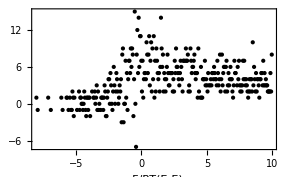

```mathematica
plotData1=ListPlot[-result,option4]
```

Fig. Chapter.FigureCaption  Monte Carlo simulation of a reversible linear sweep voltammogram. Simulation parameters: 10000 molecules and 400 time steps.

One possible way to speed the simulation up is to perform the 400 step random walk and then test to see if electron transfer occurred after the random walk has been completed. By performing the test on lists of data some speed improvement should be found. Whether or not a molecule reached the electrode surface and if so after how many steps can be found using Position. For example:

```mathematica
ClearAll[walk,reachSurface];
walk=NestList[rw+#&,10,400];
reachSurface=Flatten@Position[walk,0]
```

{111,113,115,117,119,121,129}

Rather than use If to test whether or not the electron transfer takes place note that if the random number is less than ξ/(1+ξ) then subtracting it from ξ/(1+ξ) produce a positive number and if it is greater than ξ/(1+ξ) subtracting it from ξ/(1+ξ) will produce a negative number. In other words the Sign of the resultant number will be negative or positive one respectively reflecting the oxidation state of the molecule.

```mathematica
ClearAll[state];

state={Sign[(Exp[initial-#*incr]/(1+Exp[initial-#*incr]))-RandomReal[{0,1}]]}&/@reachSurface
```

{{1},{1},{1},{1},{1},{1},{1}}

If this output initially contains positive one then this means that the molecule remained oxidized until a later encounter with the electrode surface. For an electron transfer to have taken place, either oxidation or subsequent reduction there will be a change in sign of two adjacent elements in the list state. By appending the initial oxidation state of the molecule to the list and splitting the list up into adjacent pairs it is then possible to test if the elements are the same. Tests that yield false indicates an electron transfer has taken place.

```mathematica
ClearAll[pairs];
state=Append[{1},state]//Flatten;
pairs=Partition[state,2,1]
Apply[SameQ,pairs,{1}]
```

{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}

{True,True,True,True,True,True,True}

These steps can be combined and the position of the false result returned.

```mathematica
pos=Position[Apply[SameQ,Partition[state,2,1],{1}],False]//Flatten
```

{}

Alternatively it can be noted that if the pairs of elements are unequal they will sum to zero. Therefore as an alternative and marginally faster method we could apply ListCorrelate to the data and return the positions of the zeros.

```mathematica
pos=Position[ListCorrelate[{1,1},state],0]//Flatten
```

{}

Position(s) returned correspond to the elements of the list reachSurface. The value of the elements in the list pos above indicate the number of steps (i.e. the potential) at which an electron transfer occurred. This information can be used to return a list containing the dimensionless potential and the electron transfer.

```mathematica
{initial-reachSurface⟦#⟧*incr,state⟦#+1⟧}&/@pos
```

{}

All these steps can be combined into one function.

```mathematica
ClearAll[sortData];
sortData[list_List,initial_,incr_]:=Module[{pos,state},state=Flatten@{1,{-Sign[RandomReal[{0,1}]-(Exp[initial-#*incr]/(1+Exp[initial-#*incr]))]}&/@list};
pos=Flatten@Position[Apply[SameQ,Partition[state,2,1],{1}],False];{initial-list⟦#,1⟧*incr,state⟦#+1⟧}&/@pos
]
```

After generating a large number of random walks of length 400 the list can be mapped onto the function sortData.

```mathematica
walk=NestList[rw+#&,10,400];
reachSurface=Position[walk,0]
```

{}

```mathematica
ClearAll[g,lsv1,walk,reachSurface];

Timing[
lsv1=Table[
walk=NestList[rw+#&,RandomInteger[{1,85}],400];reachSurface=Position[walk,0],{100000}];
g=sortData[#,initial,incr]&/@ lsv1;
]
```

{58.8775,Null}

Well that is a marginal improvement in speed. The output is treated using the same steps as before.

```mathematica
g1=Partition[Flatten[g],2];
g1=DeleteCases[g1,_?(#⟦2⟧==  0&) |_?(#⟦1⟧== -10.&)] ;
c1=Sort[g1];
c1=Split[c1,#1⟦1⟧== #2⟦1⟧&];
c1=If[Length[#]>1,{#⟦1,1⟧,Apply[Plus,#⟦All,2⟧]},#]&/@ c1;
result=Reverse[Partition[Flatten[c1],2]];
```

The data can be plotted and compared to a reversible voltammogram calculated using eqn (5.20) from §5.2. Data from a simulated reversible linear sweep voltammogram, cvRev.dat, is located in the Data folder. To save some time the result of a simulation with one million molecules is contained in the file monteCarloLSV.dat.

```mathematica
ClearAll[result,lsv,lsv1];

result=<<monteCarloLSV.dat;
lsv=<<cvRev.dat;

(*next adjust the y axis so that the CV and the Monte Carlo data scale accordingly*)

lsv1={#⟦1⟧,1288*#⟦2⟧}&/@lsv;
```

Figure Chapter.FigureCaption compares a Monte Carlo simulated reversible voltammogram with one simulated by numerical integration as described in Chapter 5. To compare this data with a reversible cyclic voltammogram the y values of the Monte Carlo data need to scaled. This was done following the semi-integration described below.

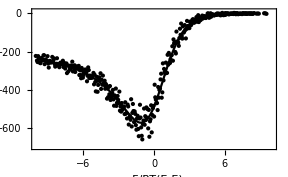

```mathematica
ListPlot[lsv1,option5,
PlotStyle-> Black,
Epilog->{Black,AbsolutePointSize[3], Point/@result}]
```

Fig. Chapter.FigureCaption  Monte Carlo simulation of a reversible linear sweep voltammogram. Points - Monte Carlo simulation. line - numerical integration of convolution integral. Simulation parameters N=10^6 molecules, and n=400 time steps.

A simulation with N=10^6 molecules and n=400 time steps (a total of 4 · 10^8steps) took approximately 225 minutes on a Macintosh 400 MHz G4. The Monte Carlo data is very noisy. The signal to noise ratio scales with N^(1/2) so that increasing the number of molecules to obtain better data requires a lot of computation time. The best way to smooth this data is by convolution. The convolution filter being used is discussed in more detail in Chapter 15.

```mathematica
ClearAll[len,kernel,data,filtData,filtData2];

(*remove potential values to leave a one dimensional list*)
data=result⟦All,2⟧;
len=50;
kernel=Table[Exp[-n^2/100]/Sqrt[2. Pi],{n,-len,len}];
kernel=kernel/(Plus@@kernel);

filtData=ListConvolve[kernel,data];

(*add potential scale back to the filtered data*)
filtData2=Transpose[{Take[result⟦All,1⟧,{len+1,Length[result]-len}],filtData}];
```

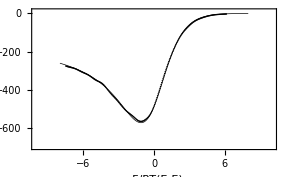

```mathematica
ListPlot[lsv1,option5,
PlotStyle-> Directive[Black,AbsoluteThickness[0.5]],
Prolog->{Black,AbsolutePointSize[1], Point/@filtData2}]
```

Fig. Chapter.FigureCaption  Smoothed Monte Carlo simulation data for a reversible linear sweep voltammogram. Points - smoothed Monte Carlo simulation. line - numerical integration of convolution integral. Simulation parameters N=10^6 molecules, and n=400 time steps.

Another way to smooth the data is to take the semi-integral of it. Semi-integration, which is also a convolution integral, is discussed in Appendix 2. The function semiIntD2 performs the semi integration of two column data. note

```mathematica
semiMC=semiIntD2[result,0.05];
semiLSV=semiIntD2[lsv,0.005];
```

The simulated current values of the Monte Carlo data are not scaled. To compare this data with a reversible cyclic voltammogram the y values of the Monte Carlo data need to scaled.

```mathematica
scale=Min[semiLSV⟦All,2⟧]/Min[semiMC⟦All,2⟧];
semiMC⟦All,2⟧=scale*semiMC⟦All,2⟧;
```

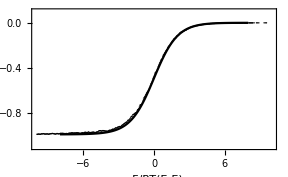

```mathematica
ListPlot[semiLSV,option6,Prolog->{Black,AbsolutePointSize[1], Point/@semiMC}]
```

Fig. Chapter.FigureCaption  Semi-integration of the simulated data shown in Fig. Chapter.FigureCaption.

### Chapter.Section.Subsection Chronoamperometric simulations

Potential step experiments can be simulated in a similar fashion to the voltammetric simulation. For a reduction from a potential step to a limiting current region this becomes relatively straight forward since it can be assumed that the molecule is reduced and not subsequently re-oxidized. The simulation therefore stops when the molecule reaches the surface.

```mathematica
ClearAll[ca1];
ca1:=Length[NestWhileList[RandomChoice[{-1,1}]+#&,RandomInteger[{0,25}],(#!=0&),1,400]]
```

Testing at each time increment becomes fairly time consuming. Computational time can be saved by simulating the random walk for the maximum number of steps (i.e. maximum length of time) and then determine how many steps were taken until the molecule first reached the surface. This can be determined by finding out the positions of zero’s in the output from the NestList function above and returning the first of these positions that is equal to one plus the number of steps taken by the molecule until it initially reached the electrode surface (the first element of the output from NestList is the starting value therefore eg. the 5th element represents 4 steps).

FirstPosition[list,0]

If no zeros exist in the data, i.e. the molecule doesn’t reach the surface Missing[NotFound] is returned.

```mathematica
FirstPosition[{1,2,3,4},0]
```

Missing[NotFound]

Therefore to avoid this we append a zero the end of the list prior to searching for the first zero in the list.

```mathematica
ClearAll[ca2];
ca2[x_]:=Module[{a},
a=Flatten@{NestList[RandomChoice[{-1,1}]+#&,RandomInteger[{1,85}],400],0};
FirstPosition[a,0]]
```

```mathematica
g=Drop[NestList[ca2,{},25],1];//Timing
```

{0.053776,Null}

The data gets sorted using the same algorithm as was used in §12.3.1. Unless a large number of time increments are used most of the molecules never actually reach the surface. We see this after the data is split.

```mathematica
c1=Sort[g];
c1=Split[c1,#1⟦1⟧== #2⟦1⟧&]
```

{{{2}},{{163}},{{240}},{{260}},{{402},{402},{402},{402},{402},{402},{402},{402},{402},{402},{402},{402},{402},{402},{402},{402},{402},{402},{402},{402},{402}}}

All the values that reflect that the molecules never reached the surface need to be dropped. In this case for 400 time steps the values of 402 should be deleted. The maximum number is 402 rather than 400 because NestList automatically adds one to the length plus a zero was added to the end of the list to ensure that the function Position would find a zero so that no error message was generated. After sorting and splitting the list as described in the previous section the data can be plotted.

```mathematica
ClearAll[g];
g=Drop[NestList[ca2,{},100000],1];//Timing
```

{15.089,Null}

```mathematica
ClearAll[c1,c2];
c1=DeleteCases[g,{402}];
c1=Sort[c1];
c1=Drop[Split[c1,#1⟦1⟧== #2⟦1⟧&],-1];
c2=Short[{#⟦1,1⟧,Length[#]}&/@ c1]
```

{{2,557},{3,296},{4,295},{5,221},«391»,{397,30},{398,24},{399,27},{400,30}}

To save some time the result of a simulation with one million molecules is contained in the file monteCarloLSV.dat.

```mathematica
ClearAll[result1];
result1=<<monteCarloChrono.dat;
```

The data should be proportional to t^(-1/2).

```mathematica
ClearAll[t];
(*equation of best fit assuming ∝ t^(-1/2)*)
eqn=Fit[Abs[result1],{t^-0.5},t];
```

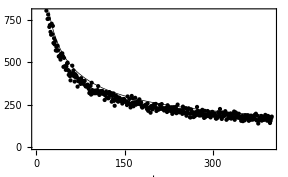

```mathematica
Plot[eqn,{t,0,400},Evaluate[option7],Epilog->{Black,AbsolutePointSize[3], Point/@result1}]
```

Fig. Chapter.FigureCaption  Simulated chronopotentiometric data. N=10^6 molecules, n=400 time time steps.

Next take the log of the data in the list result1. The slope of the log-log plot should ideally be -0.5.

```mathematica
ClearAll[x,c3,eqn2];
c3={Log[#⟦1⟧],Log[#⟦2⟧]}&/@result1;
eqn2=Fit[Abs[c3],{1,x},x]
```

8.24062-0.525756 x

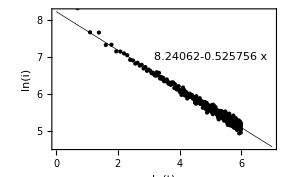

```mathematica
Plot[eqn2,{x,0,7},Evaluate[option8],Epilog->{Black,AbsolutePointSize[3], Point/@c3,Black,Text[eqn2,{5,7}]}]
```

Fig. Chapter.FigureCaption  Log-log plot of the simulated chronopotentiometric data. N=10^6 molecules, n=400 time steps.

Log-log plots can be obtained directly from lists using ListLogLogPlot.

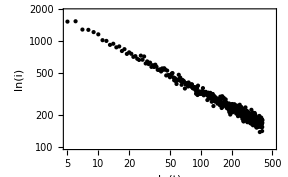

```mathematica
ListLogLogPlot[result1,option9]
```

Fig. Chapter.FigureCaption  Log-log plot of the simulated chronopotentiometric data. N=10^6 molecules, n=400 time steps.